∫_a^b √(1+df[x]^2)ⅆx

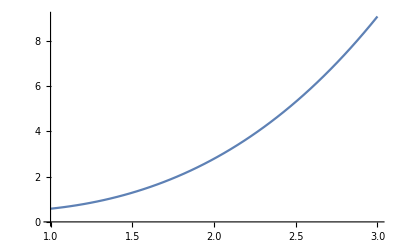

8.83333

```mathematica
(* Name: Jenny Chen *)
(* MATH2262B: Analytic Geometry and Calculus II *)
(* Mathematica Project 1 *)

(* Pg. 388, # 11-16 *)

(* 11. y = ((x^3)/3) + (1/(4x)), 1≤x≤3 *) 

a = 1;
b = 3;

f[x_]:= ((x^3)/3) + (1/(4x));
df[x_]:=f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b √(1+df[x]^2)ⅆx

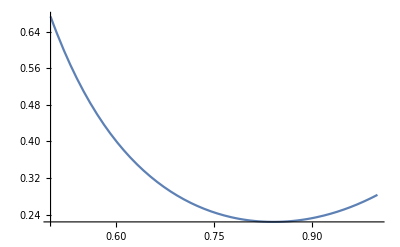

0.777083

```mathematica
(* 12. y = ((x^5)/5) + (1/(12x^3)), (1/2)≤x≤1 *)

a = (1/2);
b = 1;

f[x_] := ((x^5)/5) + (1/(12x^3));
df[x_]:=f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b √(1+f[y]^2)ⅆy

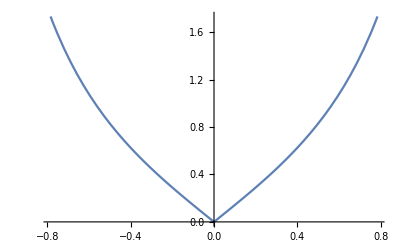

2.

```mathematica
(* 13. x = ∫_0^y Sqrt[sec[t]^4 - 1]ⅆt , (-pi/4)≤y≤(pi/4) *) 

a = (-Pi/4);
b = (Pi/4);

f[y_]:= Sqrt[Sec[y]^4 - 1];


Defer[Integrate[Sqrt[1+(f[y])^2],{y,a,b}]]

Plot[f[y],{y,a,b}]

L=NIntegrate[Sqrt[1+(f[y])^2],{y,a,b}]
```

∫_a^b √(1+f[x]^2)ⅆx

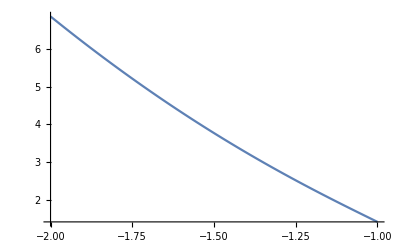

4.04145

```mathematica
(* 14. y = ∫_-2^x Sqrt[3t^4 - 1]ⅆt , -2≤x≤-1 *)

a= -2;
b= -1;

f[x_]:= Sqrt[3x^4 - 1];

Defer[Integrate[Sqrt[1+(f[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(f[x])^2],{x,a,b}]
```

∫_a^b √(1+df[x]^2)ⅆx

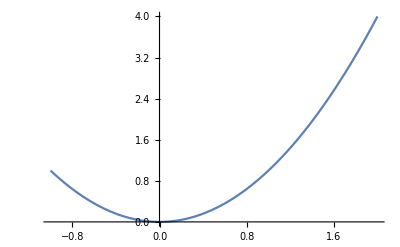

6.12573

```mathematica
(* 15. y = x^2 , -1≤x≤2 *)

a= -1;
b = 2;

f[x_] := (x^2);
df[x_] := f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b √(1+df[x]^2)ⅆx

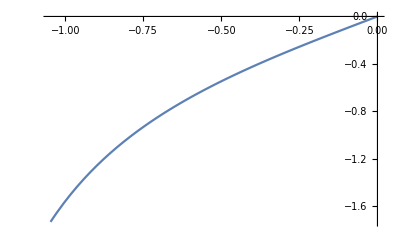

2.057

```mathematica
(* 16. y = Tan[x] , (-Pi/3)≤x≤0 *)

a= (-Pi/3);
b = 0; 
f[x_] := Tan[x];
df[x_] := f'[x]; 

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]
Plot[f[x],{x,a,b}]
L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b} ]
```

∫_a^b √(1+df[x]^2)ⅆx

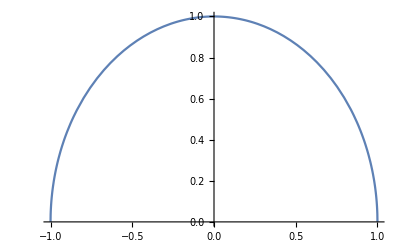

3.14159

```mathematica
(* Pg. 389, # 37-42 *)

(* 37. f(x)= Sqrt[1-(x^2)] , -1≤x≤1 *)
a = -1;
b= 1;

f[x_] := (Sqrt[1-(x^2)]);
df[x_] := f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b √(1+df[x]^2)ⅆx

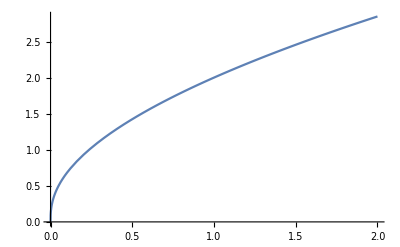

3.61416

```mathematica
(* 38. f(x)= x^(1/3) + x^(2/3) , 0≤x≤2 *)
a = 0;
b = 2;
f[x_] := (x^(1/3) + x^(2/3));
df[x_] := f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b √(1+df[x]^2)ⅆx

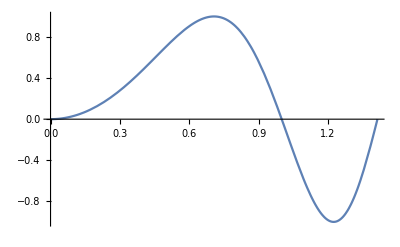

4.40635

```mathematica
(* 39. f(x)= Sin[Pi * x^2] , 0≤x≤Sqrt[2] *)
a = 0;
b= Sqrt[2];
f[x_] := (Sin[Pi * x^2]);
df[x_] := f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b √(1+df[x]^2)ⅆx

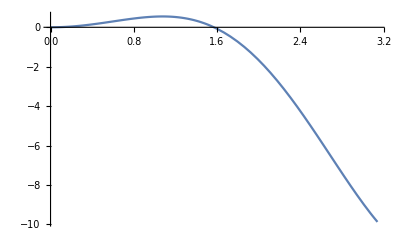

12.0189

```mathematica
(* 40. f(x)= x^2Cos[x] , 0≤x≤Pi *)
a = 0;
b= Pi;
f[x_] := (x^2Cos[x]);
df[x_] := f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b √(1+df[x]^2)ⅆx

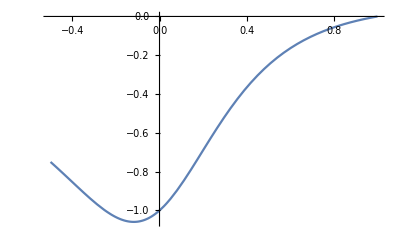

2.10892

```mathematica
(* 41. f(x)= ((x-1)/(4x^2 + 1)), ((-1/2)≤x≤1 *)
a = (-1/2);
b= 1;

f[x_] := ((x-1)/(4x^2 + 1));
df[x_] := f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b √(1+df[x]^2)ⅆx

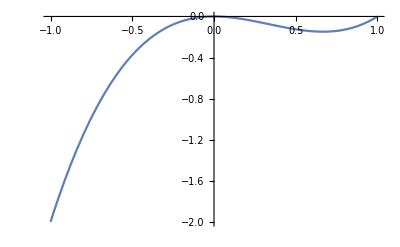

3.42491

```mathematica
(* 42. f(x)= x^3 - x^2, -1≤x≤1 *)
a= -1;
b= 1;

f[x_] := (x^3 - x^2);
df[x_] := f'[x];

Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]

L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b 2 π f[x] √(1+df[x]^2)ⅆx

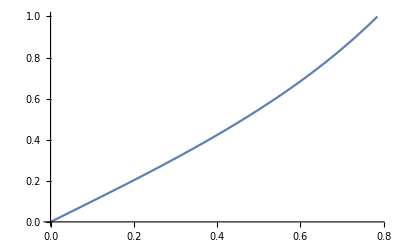

-Graphics3D-

-Graphics3D-

-Graphics3D-

3.83908

```mathematica
(* Pg. 393, # 1,2,4,6 *)

(* 1. y = Tan[x] , 0≤x≤(Pi/4), x-axis *)

a= 0;
b= (Pi/4);

f[x_]:= (Tan[x]);
df[x_]:=f'[x];
Defer[Integrate[2Pi*f[x]*Sqrt[1+(df[x])^2],{x,a,b}]]
Plot[f[x],{x,a,b}]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"x"]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"y"]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"z"]

A=NIntegrate[2Pi*f[x]*Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b 2 π f[x] √(1+df[x]^2)ⅆx

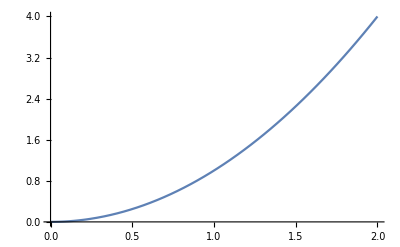

-Graphics3D-

-Graphics3D-

-Graphics3D-

53.226

```mathematica
(* 2. y = x^2, 0≤x≤2, x-axis *)

a= 0;
b= 2;

f[x_]:= x^2;
df[x_]:=f'[x];

Defer[Integrate[2Pi*f[x]*Sqrt[1+(df[x])^2],{x,a,b}]]

Plot[f[x],{x,a,b}]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"x"]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"y"]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"z"]

A=NIntegrate[2Pi*f[x]*Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b 2 π f[y] √(1+df[y]^2)ⅆy

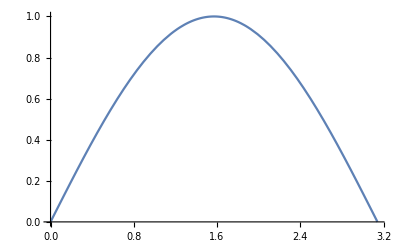

-Graphics3D-

-Graphics3D-

-Graphics3D-

14.4236

```mathematica
(* 4. x = Sin y, 0≤y≤Pi , y-axis *)
a= 0;
b= Pi;

f[y_]:= Sin[y];
df[y_]:=f'[y];

Defer[Integrate[2Pi*f[y]*Sqrt[1+(df[y])^2],{y,a,b}]]

Plot[f[y],{y,a,b}]
RevolutionPlot3D[f[y],{y,a,b},RevolutionAxis->"x"]
RevolutionPlot3D[f[y],{y,a,b},RevolutionAxis->"y"]
RevolutionPlot3D[f[y],{y,a,b},RevolutionAxis->"z"]

A=NIntegrate[2Pi*f[y]*Sqrt[1+(df[y])^2],{y,a,b}]
```

```mathematica
(* 6. y + 2 * Sqrt[y]= x , 1≤y≤2 , y-axis *)
```

∫_a^b 2 π f[y] √(1+df[y]^2)ⅆy

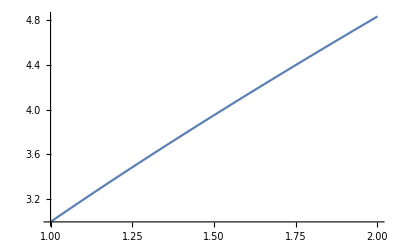

-Graphics3D-

-Graphics3D-

-Graphics3D-

51.3343

```mathematica
a= 1;
b= 2;

f[y_]:= y + 2 * Sqrt[y];
df[y_]:=f'[y];

Defer[Integrate[2Pi*f[y]*Sqrt[1+(df[y])^2],{y,a,b}]]

Plot[f[y],{y,a,b}]
RevolutionPlot3D[f[y],{y,a,b},RevolutionAxis->"x"]
RevolutionPlot3D[f[y],{y,a,b},RevolutionAxis->"y"]
RevolutionPlot3D[f[y],{y,a,b},RevolutionAxis->"z"]

A=NIntegrate[2Pi*f[y]*Sqrt[1+(df[y])^2],{y,a,b}]
```